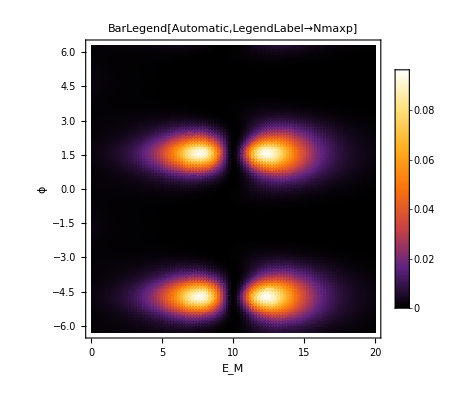

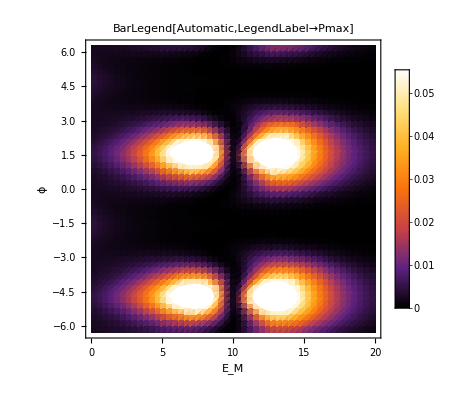

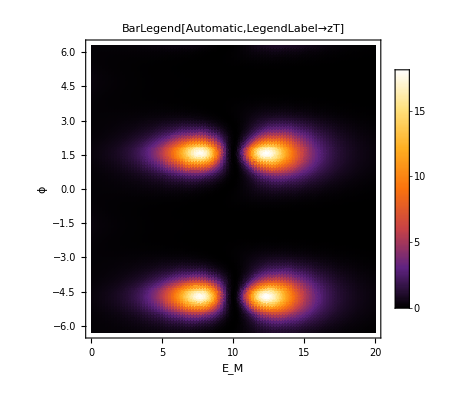

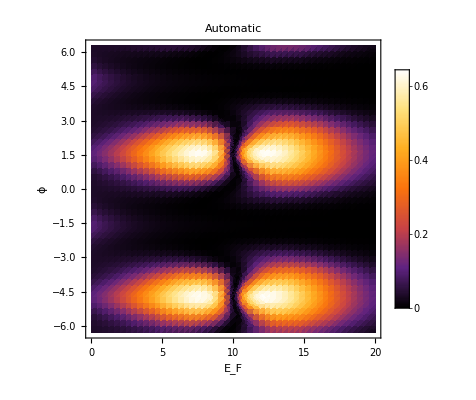

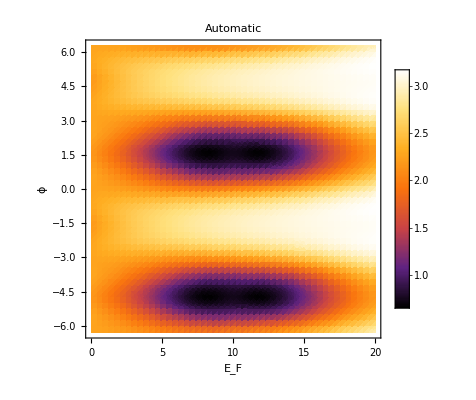

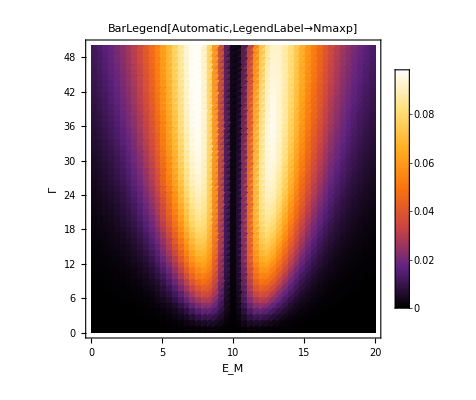

```mathematica
kbT = 1;                (*T = 115mK, E0 and Ef are in units of μeV*)
df[E0_,Ef_] := (ⅇ^((E0-Ef)/kbT)/((1+ⅇ^((E0-Ef)/kbT))^2 kbT));
(*Partial derivative of Fermi function with respect to incident electron energy*)



jk = 10





(*Defining the transmission probability*)

T1[E0_,Ef_,G1_,phi_,Em_] :=4 ⅇ^(-Im[E0+Ef+1000 phi]/1000) (Abs[(ⅇ^(ⅈ phi) (ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (E0+ⅈ G1)^2 G1^2+ⅇ^((ⅈ E0)/1000+2 ⅈ phi) G1^2 (-ⅈ E0+G1)^2+4 ⅇ^((ⅈ (3 E0+Ef))/2000) G1 (-ⅈ E0+G1) (E0^2-Em^2+ⅈ E0 G1)+4 ⅇ^((ⅈ (E0+2 Ef))/1000) (E0^2-Em^2+ⅈ E0 G1)^2+ⅇ^((ⅈ (2 E0+Ef))/1000) G1 (-ⅈ E0+G1) (2 E0^2-2 Em^2+ⅈ E0 G1+G1^2)+4 ⅇ^((ⅈ Ef)/1000) (-E0^2+Em^2-2 ⅈ E0 G1+G1^2)^2-ⅇ^((ⅈ E0)/1000) G1 (-ⅈ E0+G1) (-2 E0^2+2 Em^2-3 ⅈ E0 G1+G1^2)+4 ⅇ^((3 ⅈ (E0+Ef))/2000) (E0^4+Em^4+ⅈ E0^3 G1-Em^2 G1^2+E0^2 (-2 Em^2+G1^2)+ⅈ E0 G1 (-Em^2+G1^2))+4 ⅇ^((ⅈ (E0+Ef))/1000) (2 E0^4+2 Em^4+4 ⅈ E0^3 G1-G1^4-E0^2 (4 Em^2+G1^2)-2 ⅈ E0 (2 Em^2 G1-G1^3))+4 ⅇ^((ⅈ (E0+Ef))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3))+8 ⅇ^((ⅈ (E0+3 Ef))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3)))+(1+ⅇ^((ⅈ (E0+Ef))/2000)) (ⅇ^((ⅈ E0)/1000)+ⅇ^((ⅈ (3 E0+Ef))/2000)-ⅇ^((ⅈ E0)/1000+2 ⅈ phi)-4 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000)-4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000)-ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000)+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000)) Em (E0^2-Em^2+2 ⅈ E0 G1-G1^2) Abs[G1]-ⅇ^((ⅈ E0)/1000+ⅈ phi) (-1-4 ⅇ^((ⅈ Ef)/1000)-4 ⅇ^((ⅈ Ef)/500)-4 ⅇ^((ⅈ (E0+Ef))/2000)-3 ⅇ^((ⅈ (E0+Ef))/1000)-8 ⅇ^((ⅈ (E0+3 Ef))/2000)-ⅇ^(2 ⅈ phi)+ⅇ^((ⅈ (E0+Ef+2000 phi))/1000)) Em^2 Abs[G1]^2)/(ⅇ^((ⅈ (2 E0+Ef))/1000) (E0+ⅈ G1)^2 G1^2-2 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (E0+ⅈ G1)^2 G1^2+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (E0+ⅈ G1)^2 G1^2+8 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) G1 (-ⅈ E0+G1) (E0^2-Em^2+ⅈ E0 G1)+8 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) G1 (-ⅈ E0+G1) (E0^2-Em^2+ⅈ E0 G1)+16 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-E0^2+Em^2-2 ⅈ E0 G1+G1^2)^2-4 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) G1 (-ⅈ E0+G1) (-2 E0^2+2 Em^2-3 ⅈ E0 G1+G1^2)-4 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) G1 (-ⅈ E0+G1) (-2 E0^2+2 Em^2-3 ⅈ E0 G1+G1^2)+8 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (2 E0^4+2 Em^4+4 ⅈ E0^3 G1-G1^4-E0^2 (4 Em^2+G1^2)-2 ⅈ E0 (2 Em^2 G1-G1^3))+16 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3))+16 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3))+4 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-1+ⅇ^((ⅈ Ef)/1000)) (1+ⅇ^((ⅈ Ef)/1000)+ⅇ^((ⅈ (E0+Ef))/2000)) (-1+ⅇ^(2 ⅈ phi)) Em (E0^2-Em^2+2 ⅈ E0 G1-G1^2) Abs[G1]+ⅇ^((ⅈ E0)/1000) (-ⅇ^((ⅈ (E0+Ef))/1000)+8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi)+4 ⅇ^((ⅈ Ef)/500+2 ⅈ phi)+4 ⅇ^(2 ⅈ phi)+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000)+8 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000)-ⅇ^((ⅈ (E0+Ef+4000 phi))/1000)+8 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000)) Em^2 Abs[G1]^2)])^2+4 ⅇ^(-Im[E0]/1000-2 Im[phi]) (Abs[(ⅇ^((ⅈ E0)/2000) G1 (-ⅈ E0+G1) (ⅇ^((ⅈ (3 E0+2 Ef))/2000) (-E0^2+Em^2-ⅈ E0 G1)+ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (-E0^2+Em^2-ⅈ E0 G1)+ⅇ^((ⅈ (E0+2 Ef))/2000) (E0^2-Em^2+ⅈ E0 G1)+2 ⅇ^((ⅈ (E0+4 Ef))/2000) (E0^2-Em^2+ⅈ E0 G1)+2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (E0^2-Em^2+ⅈ E0 G1)+ⅇ^((ⅈ (E0+2 Ef+4000 phi))/2000) (E0^2-Em^2+ⅈ E0 G1)+2 ⅇ^((3 ⅈ Ef)/2000) (E0^2-Em^2+2 ⅈ E0 G1-G1^2)+2 ⅇ^((ⅈ Ef)/2000+2 ⅈ phi) (E0^2-Em^2+2 ⅈ E0 G1-G1^2)+ⅇ^((ⅈ (2 E0+3 Ef))/2000) (E0^2-Em^2+G1^2)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0^2-Em^2+G1^2)+ⅇ^((ⅈ (2 E0+Ef))/2000) (-E0^2+Em^2-2 ⅈ E0 G1+G1^2)+ⅇ^((ⅈ (2 E0+3 Ef+4000 phi))/2000) (-E0^2+Em^2-2 ⅈ E0 G1+G1^2))+2 ⅇ^(ⅈ phi) (ⅇ^((ⅈ E0)/1000)-2 ⅇ^((ⅈ Ef)/1000)-ⅇ^((ⅈ (E0+Ef))/2000)+ⅇ^((3 ⅈ (E0+Ef))/2000)+ⅇ^((ⅈ (3 E0+Ef))/2000)+ⅇ^((ⅈ (E0+2 Ef))/1000)-ⅇ^((ⅈ (E0+3 Ef))/2000)) Em (E0^2-Em^2+2 ⅈ E0 G1-G1^2) Abs[G1]+ⅇ^((ⅈ E0)/1000) (ⅇ^((ⅈ Ef)/1000)+2 ⅇ^((ⅈ Ef)/500)-ⅇ^((ⅈ (E0+Ef))/1000)+2 ⅇ^((ⅈ (E0+3 Ef))/2000)+ⅇ^((ⅈ Ef)/1000+2 ⅈ phi)+2 ⅇ^(2 ⅈ phi)-ⅇ^((ⅈ (E0+Ef+2000 phi))/1000)+2 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000)) Em^2 Abs[G1]^2)/(ⅇ^((ⅈ (2 E0+Ef))/1000) (E0+ⅈ G1)^2 G1^2-2 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (E0+ⅈ G1)^2 G1^2+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (E0+ⅈ G1)^2 G1^2+8 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) G1 (-ⅈ E0+G1) (E0^2-Em^2+ⅈ E0 G1)+8 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) G1 (-ⅈ E0+G1) (E0^2-Em^2+ⅈ E0 G1)+16 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-E0^2+Em^2-2 ⅈ E0 G1+G1^2)^2-4 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) G1 (-ⅈ E0+G1) (-2 E0^2+2 Em^2-3 ⅈ E0 G1+G1^2)-4 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) G1 (-ⅈ E0+G1) (-2 E0^2+2 Em^2-3 ⅈ E0 G1+G1^2)+8 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (2 E0^4+2 Em^4+4 ⅈ E0^3 G1-G1^4-E0^2 (4 Em^2+G1^2)-2 ⅈ E0 (2 Em^2 G1-G1^3))+16 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3))+16 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (E0^4+3 ⅈ E0^3 G1+Em^2 (Em^2+G1^2)-E0^2 (2 Em^2+3 G1^2)-ⅈ E0 (3 Em^2 G1+G1^3))+4 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-1+ⅇ^((ⅈ Ef)/1000)) (1+ⅇ^((ⅈ Ef)/1000)+ⅇ^((ⅈ (E0+Ef))/2000)) (-1+ⅇ^(2 ⅈ phi)) Em (E0^2-Em^2+2 ⅈ E0 G1-G1^2) Abs[G1]+ⅇ^((ⅈ E0)/1000) (-ⅇ^((ⅈ (E0+Ef))/1000)+8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi)+4 ⅇ^((ⅈ Ef)/500+2 ⅈ phi)+4 ⅇ^(2 ⅈ phi)+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000)+8 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000)-ⅇ^((ⅈ (E0+Ef+4000 phi))/1000)+8 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000)) Em^2 Abs[G1]^2)])^2




(*Different values of Em in μeV*)
Emaj = 10;


(*Different elements of the Onsager matrix, change last input of transmission probability to change Em*)
LeTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,G1,phi,Em])(df[E0/kbT,Ef/kbT])
LeVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=( ((E0 - (Ef))/kbT)^(0)) (T1[(E0),Ef,G1,phi,Em])(df[E0/kbT,Ef/kbT])
LhVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,G1,phi,Em])(df[E0/kbT,Ef/kbT])
LhTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=( ((E0 - (Ef))/kbT)^(2)) (T1[(E0),Ef,G1,phi,Em])(df[E0/kbT,Ef/kbT])

LeV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ LeVv[(E0), fer,Em,phi, G1], {E0, -Infinity, Infinity}]

LeT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[LeTt[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

LhV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[LhVv[(E0), fer, Em,phi, G1]        , {E0, -Infinity, Infinity}]

LhT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[LhTt[(E0), fer, Em,phi, G1]  , {E0, -Infinity, Infinity}]


(*Thermoelectric parameters acquired from the Onsager matrix elements*)
k[fer_, Em_, phi_, G1_] :=(1/(2))((LeT[fer, Em, phi, G1])^2/(2*(LeV[fer, Em, phi, G1]*LhT[fer, Em, phi, G1])-(LeT[fer, Em, phi, G1]*LhV[fer, Em, phi, G1])))
p[fer_, Em_, phi_, G1_] := (1/(4*1)) * ((LeT[fer, Em, phi, G1])^2)/LeV[fer, Em, phi, G1]
S[fer_, Em_, phi_, G1_] := -LeT[fer, Em, phi, G1]/LeV[fer, Em, phi, G1]
kappa[fer_, Em_, phi_, G1_] := ((LeV[fer, Em, phi, G1]*LhT[fer, Em, phi, G1] - LhV[fer, Em, phi, G1]*LeT[fer, Em, phi, G1])/ (LeV[fer, Em, phi, G1]))/3.285
P[fer_, Em_, phi_, G1_] := (LhV[fer, Em, phi, G1]/LeV[fer, Em, phi, G1])(1)
zT[fer_, Em_, phi_, G1_] := 11.5*(LeV[fer, Em, phi, G1](S[fer, Em, phi, G1])^2/(kappa[fer, Em, phi, G1]))/(1)
Nmax[fer_, Em_, phi_, G1_]:=(Sqrt[z0 [fer, Em, phi, G1] + 1] - 1)/(Sqrt[z0[fer, Em, phi, G1] + 1] + 1)
Pmaxr[fer_, Em_, phi_, G1_]:= Sqrt[(LhT[fer, Em, phi, G1])(LeV[fer, Em, phi, G1]*LhT[fer, Em, phi, G1] - LhV[fer, Em, phi, G1]*LeT[fer, Em, phi, G1])/(LeV[fer, Em, phi, G1])]



DensityPlot[{k[10, em, phi, 20]}, {em, 0,20},{phi, -2*Pi, 2*Pi}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["ϕ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{p[10, em, phi, 20]}, {em, 0,20},{phi, -2*Pi, 2*Pi}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["ϕ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Pmax"], PlotLabel->"Pmax",PlotRange->All, PlotPoints->30]
DensityPlot[{zT[10, em, phi, 20]}, {em, 0,20},{phi, -2*Pi, 2*Pi}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["ϕ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"zT"], PlotLabel->"zT",PlotRange->All, PlotPoints->30]
DensityPlot[{Nmax[10, em, phi, 20]}, {em, 0,20},{phi, -2*Pi, 2*Pi}, ColorFunction->"SunsetColors",PlotLegends->Automatic, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmax"], PlotLabel->"Nmax",PlotRange->All, PlotPoints->30]
DensityPlot[{Pmaxr[10, em, phi, 10]}, {em, 0,20},{phi, -2*Pi, 2*Pi}, ColorFunction->"SunsetColors",PlotLegends->Automatic,  PlotRange->All, PlotPoints->30]


DensityPlot[{k[10, em, 1.57,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{p[10, em, 1.57,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{zT[10, em, 1.57,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{Nmax[10, em, 1.57,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{Pmaxr[10, em, 1,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
DensityPlot[{Nmax[10, em, 1,gamma]}, {em, 0,20},{gamma, 0, 50}, ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameLabel->{Text[Style["E_M", FontSize->20]], Text[Style["Γ", FontSize->20]]}, PlotLabel->BarLegend[ Automatic,LegendLabel->"Nmaxp"], PlotLabel->"Nmaxp",PlotRange->All, PlotPoints->30]
```

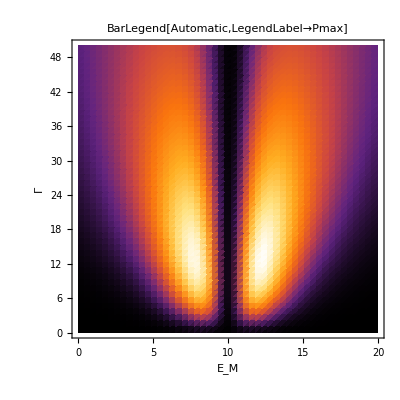
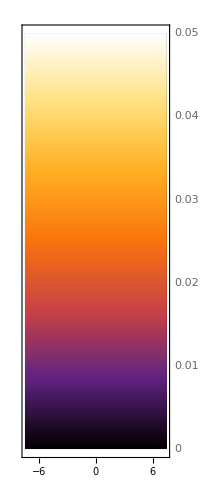

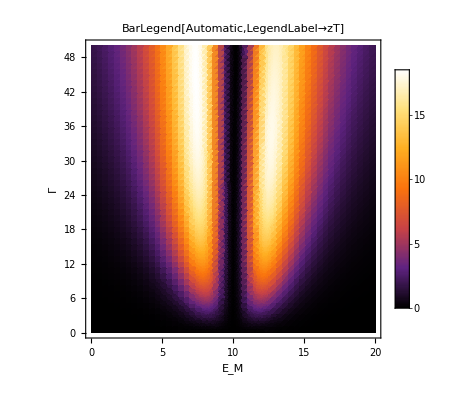

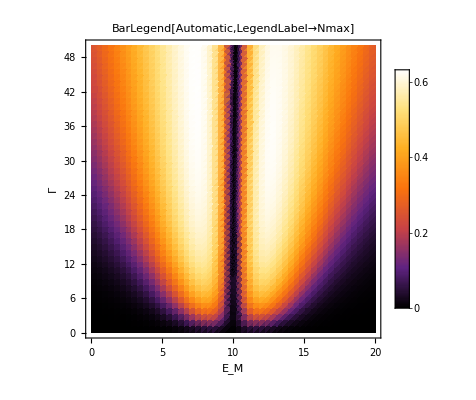

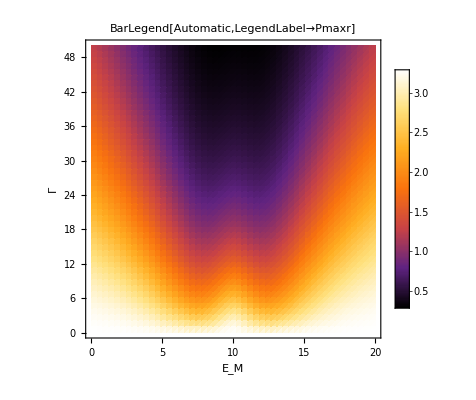

-Graphics-